```mathematica
(* Clear all variables and install MaTeX *)
Clear["Global`*"]
ResourceFunction["MaTeXInstall"][];
Needs["MaTeX`"]
```

```mathematica
(* Define the Lobatto IIIA and IIIB tableaux *)
a1 = {{0,0,0},{5/24,1/3,-1/24},{1/6,2/3,1/6}};
b1= {1/6,2/3,1/6};
a2 = {{1/6,-1/6,0},{1/6,1/3,0},{1/6,5/6,0}};
b2 = {1/6,2/3,1/6};
c={0,1/2,1};
```

```mathematica
(* Define the embedded NPRK method, differing only in the b matrix. bdiag is the method with diagonal b, bfull is the method with nondiagonal b *)
a[i_,j_,k_]:=a[i,j,k]=a1[[i,j]]/3 + a2[[i,k]]/3 - c[[i]]/9
bfull[i_,j_]:=bfull[i,j]=b1[[i]]/3 + b2[[j]]/3 - 1/9
bdiagmatrix = DiagonalMatrix[b1];
bdiag[i_,j_]:=bdiag[i,j]=bdiagmatrix[[i,j]]
```

```mathematica
(* Module which implements one time step of the embedded method for the Lotka-Volterra system
u' = u - guv, v' = v + guv from initial condition (u,v)=(x0,y0), timestep h and coupling g *)
updatefull[x0_,y0_,h_,g_]:=updatefull[x0,y0,h,g]= Module[{u=x0,v=y0,X,Y,t1,t2,xf,yf,xd,yd},
{u,v}={u,v};
t1=Table[X[i]== u + h Sum[a[i,j,k]X[k] - g a[i,j,k]X[j]Y[k],{j,1,3},{k,1,3}],{i,1,3}];
t2=Table[Y[i]==v + h Sum[a[i,j,k]Y[j] + g a[i,j,k]X[k]Y[j],{j,1,3},{k,1,3}],{i,1,3}];
{X[1],X[2],X[3],Y[1],Y[2],Y[3]}={X[1],X[2],X[3],Y[1],Y[2],Y[3]}/.FindRoot[Flatten[{t1,t2}],{{X[1],x0},{X[2],x0},{X[3],x0},{Y[1],y0},{Y[2],y0},{Y[3],y0}}];
xf = x0 + h Sum[bfull[i,j]X[j]- g bfull[i,j]X[i]Y[j],{i,1,3},{j,1,3}];
yf = y0 + h Sum[bfull[i,j]Y[j]+g bfull[i,j]X[j]Y[i],{i,1,3},{j,1,3}];
xd = x0 + h Sum[bdiag[i,j]X[j]- g bdiag[i,j]X[i]Y[j],{i,1,3},{j,1,3}];
yd = y0 + h Sum[bdiag[i,j]Y[j]+g bdiag[i,j]X[j]Y[i],{i,1,3},{j,1,3}];
{xf,yf,xd,yd}
]
```

### Embedded estimate: scale test with respect to α for various choices of h

```mathematica
(* Compute the embedded estimate as a function of α for various choices of h *)
```

```mathematica
terr[h_]:=terr[h]=Table[{g,Abs[updatefull[1,1,h,g][[1]]-updatefull[1,1,h,g][[3]]]+Abs[updatefull[1,1,h,g][[2]]-updatefull[1,1,h,g][[4]]]},{g,0,10,0.001}];
```

```mathematica
ListPlot[{testData1,testData2,testData3},PlotMarkers->{{●,10},{▲,10},{■,10}}]
```

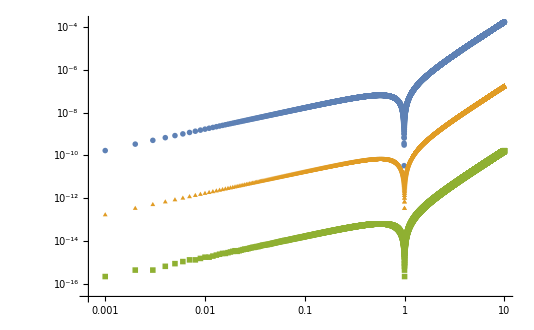

```mathematica
ListLogLogPlot[{terr[10^-2], terr[10^-3], terr[10^-4]},
AxesLabel->{MaTeX["\\alpha",FontSize->20],MaTeX["\\|y_1 - \\widetilde{y_1}\\|_{l^1}",FontSize->20]},
PlotMarkers->{{"*",17},{▲,12},{■,12}}, PlotLegends->{MaTeX["h = 10^{-2}",FontSize->20], MaTeX["h = 10^{-3}",FontSize->20], MaTeX["h = 10^{-4}",FontSize->20]}]
```

### Embedded estimate: scale test with respect to h for various values of α

```mathematica
(* Compute the embedded estimate as a function of h for various values of α *)
(* additionaly, takes log log of the data and determines the slope by linear regression *)
```

```mathematica
dterr[g_] :=dterr[g]=Table[{h,Abs[updatefull[1,1,h,g][[1]]-updatefull[1,1,h,g][[3]]]+Abs[updatefull[1,1,h,g][[2]]-updatefull[1,1,h,g][[4]]]},{h,0.0002,0.005,0.0001}];
loglogdterr[g_]:=loglogdterr[g]= Table[{Log[dterr[g][[i,1]]],Log[dterr[g][[i,2]]]},{i,1,Length[dterr[1]]-1}];
fitslope[g_]:=fitslope[g]=D[Normal[LinearModelFit[loglogdterr[g],x,x]],x]
```

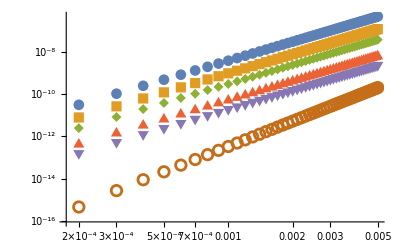

```mathematica
ListLogLogPlot[{dterr[3.0],dterr[2.0],dterr[1.5],dterr[0.5],dterr[0.1], dterr[1.0]},PlotMarkers->Automatic,PlotRange->All,PlotLegends->
{MaTeX["\\alpha = 3.0: \\text{Slope }"<>ToString[fitslope[3.0]],FontSize->15],
MaTeX["\\alpha = 2.0: \\text{Slope }"<>ToString[fitslope[2.0]],FontSize->15],
MaTeX["\\alpha = 1.5: \\text{Slope }"<>ToString[fitslope[1.5]],FontSize->15],
MaTeX["\\alpha = 0.5: \\text{Slope }"<>ToString[fitslope[0.5]],FontSize->15],
MaTeX["\\alpha = 0.1: \\text{Slope }"<>ToString[fitslope[0.1]],FontSize->15],
MaTeX["\\alpha = 1.0: \\text{Slope }"<>ToString[fitslope[1.0]],FontSize->15]},
AxesLabel->{MaTeX["h",FontSize->20],MaTeX["\\|y_1 - \\widetilde{y_1}\\|_{l^1}",FontSize->20]}
]
```

### Convergence test with respect to h for Method 1 and Method 2

```mathematica
(* Convergence test to verify both methods exhibit correct order with respect to timestep h *)
```

```mathematica
Clear[xref,yref,xd,yd,xf,yf,errordtdiag,errordtfull]
```

```mathematica
T=1.0;
errordtdiag={};
errordtfull = {};
alpha=2.0; (* change to other values of α *)
```

```mathematica
(* the same Module as updatefull above but does not save the outputs to memory *)
updatefull2[x0_,y0_,h_,g_]:= Module[{u=x0,v=y0,X,Y,t1,t2,xf,yf,xd,yd},
{u,v}={u,v};
t1=Table[X[i]== u + h Sum[a[i,j,k]X[k] - g a[i,j,k]X[j]Y[k],{j,1,3},{k,1,3}],{i,1,3}];
t2=Table[Y[i]==v + h Sum[a[i,j,k]Y[j] + g a[i,j,k]X[k]Y[j],{j,1,3},{k,1,3}],{i,1,3}];
{X[1],X[2],X[3],Y[1],Y[2],Y[3]}={X[1],X[2],X[3],Y[1],Y[2],Y[3]}/.FindRoot[Flatten[{t1,t2}],{{X[1],x0},{X[2],x0},{X[3],x0},{Y[1],y0},{Y[2],y0},{Y[3],y0}}];
xf = x0 + h Sum[bfull[i,j]X[j]- g bfull[i,j]X[i]Y[j],{i,1,3},{j,1,3}];
yf = y0 + h Sum[bfull[i,j]Y[j]+g bfull[i,j]X[j]Y[i],{i,1,3},{j,1,3}];
xd = x0 + h Sum[bdiag[i,j]X[j]- g bdiag[i,j]X[i]Y[j],{i,1,3},{j,1,3}];
yd = y0 + h Sum[bdiag[i,j]Y[j]+g bdiag[i,j]X[j]Y[i],{i,1,3},{j,1,3}];
{{xf,yf},{xd,yd}}
]
```

```mathematica
(* compute the reference solution using Method 1 with a smaller timestep than the range of h in the convergence test *)
refsteps = 10000;
xref[0]=1; yref[0]=1;
For[n=1,n<=refsteps, n++,
dt = T/refsteps;
t[n]=n*dt;
xref[n]=xref[n-1];
yref[n] = yref[n-1];
{xref[n],yref[n]} = updatefull2[xref[n],yref[n],dt,alpha][[2]];
];
xreffinal = xref[refsteps];
yreffinal = yref[refsteps];
```

```mathematica
(* alternatively, the reference solution can be computed using RK45 with a MaxStepSize h = 10^-5; uncomment the block of code below to use this for the reference solution instead *)
(* 
Fehlbergamat={{1/4},{3/32,9/32},{1932/2197,-7200/2197,7296/2197},{439/216,-8,3680/513,-845/4104},{-8/27,2,-3544/2565,1859/4104,-11/40}};
Fehlbergbvec={25/216,0,1408/2565,2197/4104,-1/5,0};
Fehlbergcvec={1/4,3/8,12/13,1,1/2};
Fehlbergevec={-1/360,0,128/4275,2197/75240,-1/50,-2/55};
FehlbergCoefficients[4,p_]:=N[{Fehlbergamat,Fehlbergbvec,Fehlbergcvec,Fehlbergevec},p];
Fehlberg45={"ExplicitRungeKutta","Coefficients"->FehlbergCoefficients,"DifferenceOrder"->4,"EmbeddedDifferenceOrder"->5,"StiffnessTest"->False};
sol=NDSolve[{u'[t]==u[t]-alpha*u[t]*v[t],v'[t]==v[t]+alpha*u[t]*v[t], u[0]==1,v[0]==1},{u,v},{t,0,1},Method->Fehlberg45,MaxStepSize->10^-5];
{xreffinal,yreffinal}={u[1],v[1]}/.sol[[1]]; 
*)
```

```mathematica
(* compute the solution at the final time from Method 1, letting h vary *)
xd[0]=1; yd[0]=1;
For[nstep = 200, nstep <= 1000, nstep += 25, 
For[n=1,n<=nstep, n++,
dt = T/nstep;
xd[n]=xd[n-1];
yd[n] = yd[n-1];
{xd[n],yd[n]} = updatefull2[xd[n],yd[n],dt,alpha][[2]];
];
errordtdiag = Append[errordtdiag,{dt,Abs[xd[nstep]-xreffinal]+Abs[yd[nstep]-yreffinal]}];
]
```

```mathematica
(* compute the solution at the final time from Method 2, letting h vary *)
xf[0]=1; yf[0]=1;
For[nstep = 200, nstep <=  1000, nstep += 25, 
For[n=1,n<=nstep, n++,
dt = T/nstep;
xf[n]=xf[n-1];
yf[n] = yf[n-1];
{xf[n],yf[n]} = updatefull2[xf[n],yf[n],dt,alpha][[1]];
];
errordtfull = Append[errordtfull,{dt,Abs[xf[nstep]-xreffinal]+Abs[yf[nstep]-yreffinal]}];
]
```

```mathematica
(* take log log of the data and use a linear fit to obtain the slope *)
logerrordtdiag= Table[{Log[errordtdiag[[i,1]]],Log[errordtdiag[[i,2]]]},{i,1,Length[errordtdiag]}];
logerrordtfull= Table[{Log[errordtfull[[i,1]]],Log[errordtfull[[i,2]]]},{i,1,Length[errordtfull]}];
dtdiagslope = D[Normal[LinearModelFit[logerrordtdiag,x,x]],x];
dtfullslope = D[Normal[LinearModelFit[logerrordtfull,x,x]],x];
```

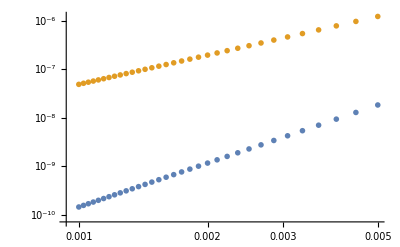

```mathematica
ListLogLogPlot[{errordtdiag, errordtfull},
PlotMarkers->{"OpenMarkers",8},
AxesLabel->{MaTeX["h",FontSize->15],MaTeX["\\text{Reference Error}",FontSize->15]},
PlotLegends->
{MaTeX["\\text{Method 1: Slope }"<>ToString[NumberForm[dtdiagslope,{7,5}]],FontSize->15], 
MaTeX["\\text{Method 2: Slope }"<>ToString[NumberForm[dtfullslope,{7,5}]],FontSize->15]}, 
PlotLabel->MaTeX["\\alpha = "<>ToString[NumberForm[alpha]],FontSize->15]]
```